## This program gets the natural response (V_s=0) of a simple parallel RLC circuit with no external source.

### τ = 1/(ω(-ζ±√(ζ^2-1))) Critically Damped Example Values: (L & C must be large for τ to be small enough to graph) L=C, R=0.5; Underdamped Example Values: R = 500kΩ, C = 6uF, L = 9nH; Overdamped Example Values: R = 0.3, C = L = 1;

ζ= 1.66667 > 1 → overdamped

V_c(t) = 3. ⅇ^(-3.33333 t) (-0.666667 ⅇ^(0.333333 t)+1. ⅇ^(3. t))

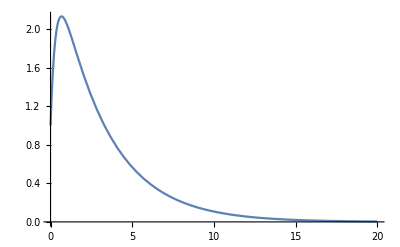

i_c(t) = -10. ⅇ^(-3.33333 t) (-0.666667 ⅇ^(0.333333 t)+1. ⅇ^(3. t))+3. ⅇ^(-3.33333 t) (-0.222222 ⅇ^(0.333333 t)+3. ⅇ^(3. t))

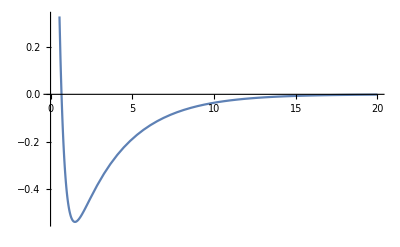

i_L(t) = 0.666667 ⅇ^(-3. t)-9. ⅇ^(-0.333333 t)

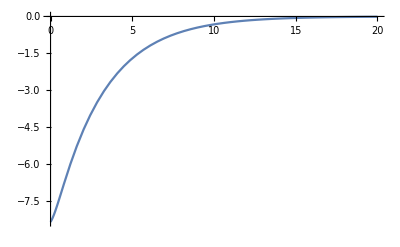

i_R(t) = 10. ⅇ^(-3.33333 t) (-0.666667 ⅇ^(0.333333 t)+1. ⅇ^(3. t))

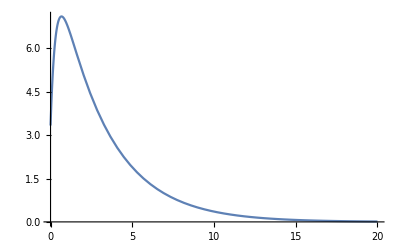

```mathematica
(*This Program gets the natural response of a simple parallel RLC circuit with no external source*)
Clear["Global`*"]
R = Input["Enter The Value Of Resistance"];
Capacitor=Input["Enter The Value Of Capacitance"];
L= Input["Enter The Value Of L"];
ωc=1/(√(L Capacitor));
ζ = 1/(2 ωc R Capacitor);
eqn1=V''[t]+2 ζ ωc V'[t]+ωc^2 V[t]==0;
capVoltage = DSolve[{eqn1, V[0]==1, V'[0]==5},V[t],t][[1]];
Vc[t_]:=V[t]/.capVoltage
inductorCurrent=1/L∫Vc[t]ⅆt;
If[ζ<1,output=StringForm["ζ= `` < 1 → underdamped", ζ], If[ζ>1, output=StringForm["ζ= `` > 1 → overdamped", ζ], output=StringForm["ζ=1 →  critically damped", ζ]]];
Style[output,Blue,20, Bold]
Style[StringForm["V_c(t) = ``", Vc[t]], Blue, 18]

Plot[Vc[t],{t,0,20}, PlotRange->Automatic]
CapacitorCurrent=Capacitor D[Vc[t],t];

ic[t_]:=CapacitorCurrent;
Style[StringForm["i_c(t) = ``", ic[t]], Blue, 18]
Plot[ic[t],{t,0,20},  PlotRange->Automatic]

i[t_]:=inductorCurrent;
Style[StringForm["i_L(t) = ``",i[t]], Blue, 18]
Plot[i[t],{t,0,20},  PlotRange->Automatic]

ResistorCurrent=1/R Vc[t];
iR[t_]:=ResistorCurrent;
Style[StringForm["i_R(t) = ``", iR[t]], Blue, 18]
Plot[iR[t],{t,0,20},  PlotRange->Automatic]
```

## This program gets the natural response (V_s=0) of a simple series RLC circuit with no external source.

### τ = 1/(ω(-ζ±√(ζ^2-1))) Critically Damped Example Values: (L & C must be large for τ to be small enough to graph) L=C=2, R=2 Underdamped Example Values: R = 0.3, C = L = 2 Overdamped Example Values : R = 5, C = 4, L = 4

ζ= 5/2 > 1 → overdamped

i_L(t) = 1/42 ⅇ^(-1/8 (5+√21) t) (21+43 √21+(21-43 √21) ⅇ^((√21 t)/4))

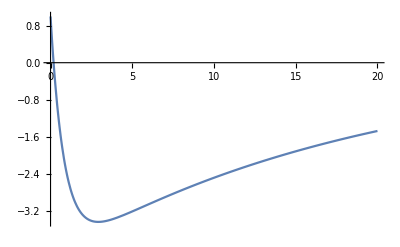

V_L(t) = 1/21 ⅇ^(-1/8 (5+√21) t) (-252-59 √21+(-252+59 √21) ⅇ^((√21 t)/4))

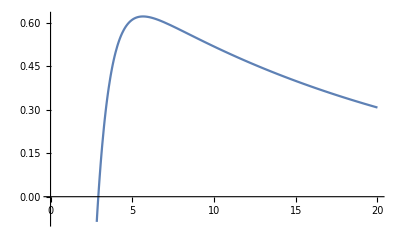

V_R(t) = 5/42 ⅇ^(-1/8 (5+√21) t) (21+43 √21+(21-43 √21) ⅇ^((√21 t)/4))

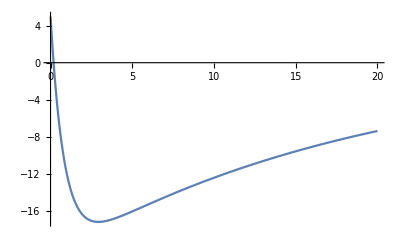

V_c(t) = 1/21 ⅇ^(-1/8 (5+√21) t) (-252-59 √21+(-252+59 √21) ⅇ^((√21 t)/4))

-Graphics-

```mathematica
Clear["Global`*"]

R =Input["Enter The Value Of Resistance"];
Capacitor=Input["Enter The Value Of Capacitance"];
L= Input["Enter The Value Of L"];
ω= 1/(√(L Capacitor));
ζ=R/(2 ω L);
eqn2 =r''[t]+2 ζ ω r'[t]+ω^2 r[t]==0;
inductorCurrent = DSolve[{eqn2,r[0]==1,r'[0]==-6},r[t],t][[1]];
iL[t_]:=r[t]/.inductorCurrent//Simplify;
If[ζ<1,output=StringForm["ζ= `` < 1 → underdamped", ζ], If[ζ>1, output=StringForm["ζ= `` > 1 → overdamped", ζ], output=StringForm["ζ=1 →  critically damped", ζ]]];
Style[output,Blue,20, Bold]
Style[StringForm["i_L(t) = ``", iL[t]], Blue, 18]
Plot[iL[t],{t,0,20},  PlotRange->Automatic]

ResistorVoltage = R*iL[t]//Simplify;
inductorVoltage = L D[iL[t],t]//Simplify;

VL[t_]:=inductorVoltage;
Style[StringForm["V_L(t) = ``", VL[t]], Blue, 18]
Plot[VL[t],{t,0,20},  PlotRange->Automatic]

VR[t_]:=ResistorVoltage;
Style[StringForm["V_R(t) = ``", VR[t]], Blue, 18]
Plot[VR[t],{t,0,20},  PlotRange->Automatic]

CapVoltage = Capacitor D[iL[t],t]//Simplify;

Vc[t_]:=CapVoltage;
Style[StringForm["V_c(t) = ``", Vc[t]], Blue, 18]
Plot[Vc[t],{t,0,20},  PlotRange->Automatic]
```